## Study the behavior of the oscillator frequencies ω_1 and ω_2

```mathematica
ClearAll["Global`*"]
```

```mathematica
S[I_,j_]:=(2I-1-2j)/(2I-1);
SP[I_,j_]:=(2j-2I-1)/(2j-1);
T[j_,γ_]:=1/(j(j+1))Sqrt[3](Sqrt[3]Cos[γ]+Sin[γ]);
TP[j_,γ_]:=1/(j(j+1))2Sqrt[3]Sin[γ];
```

### Create the omega sub-terms

### Nuclear total spin -> i Single-particle spin -> j

```mathematica
st1[i_,j_,a1_,a3_]:=(2i-1)(a3-a1)+2*j*a1;
st2[i_,j_,a1_,a2_]:=(2i-1)(a2-a1)+2*j*a1;
st3[i_,j_,a1_,a3_,v_,γ_]:=(2j-1)(a3-a1)+2*i*a1+v*(2j-1)/(j(j+1))Sqrt[3](Sqrt[3]Cos[γ]+Sin[γ]);
st4[i_,j_,a1_,a2_,v_,γ_]:=(2j-1)(a2-a1)+2i*a1+v*(2j-1)/(j(j+1))2Sqrt[3]*Sin[γ];
```

```mathematica
omega1[i_,j_,a1_,a2_,a3_]:=(st1[i,j,a1,a3]*st2[i,j,a1,a2])^(1/2);
omega2[i_,j_,a1_,a2_,a3_,v_,γ_]:=(st3[i,j,a1,a3,v,γ])^(1/2)*(st4[i,j,a1,a2,v,γ])^(1/2);
```

### Numerical interpretation

```mathematica
j0=13/2;
A1=0.05;
V=3;
γ=25*π/180;
```

### Create numerical data

```mathematica
st1[3/2,j0,A1,5*A1*S[3/2,j0]]
st2[3/2,j0,A1,2*A1*S[3/2,j0]]
omega1[3/2,j0,A1,2*A1*S[3/2,j0],5*A1*S[3/2,j0]]
```

-2.2

-0.55

1.1

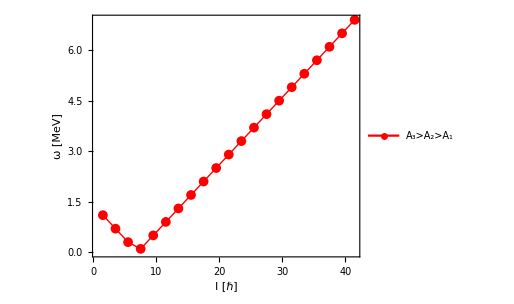

```mathematica
data1=Table[{i,omega1[i,j0,A1,2*A1*S[i,j0],5*A1*S[i,j0]]},{i,3/2,85/2,2}];
fig1=ListPlot[{data1},Joined->True,PlotMarkers->{Automatic, Medium},Frame->True,Axes->False,FrameStyle->Directive[Black, Thick],PlotStyle->{{Red,Thick}},AspectRatio->0.8,FrameLabel->{"I [ℏ]","ω [MeV]"},LabelStyle->{19,Bold,Black,FontFamily->"Arial"},PlotLegends->Placed[{"A_3>A_2>A_1"},{0.4,0.8}],PlotRange->All,ImageSize->380];
Show[fig1]
Export["/Users/basavyr/Documents/Work/DFT/mathematica-useful-algorithms/Physics/wobbling-frequency-algebraic/omega-1-2-frequencies.pdf",Show[fig1]];
```